```mathematica
{{Rx[α_] := {{1, 0, 0}, {0, Cos[α], -Sin[α]}, {0, Sin[α], Cos[α]}};
Ry[α_] := {{Cos[α], 0, Sin[α]}, {0, 1, 0}, {-Sin[α], 0, Cos[α]}};
Rz[α_] := {{Cos[α], -Sin[α], 0}, {Sin[α], Cos[α], 0}, {0, 0 , 1}};

Minv = Inverse[Rz[β]];
Mzinv = Simplify[Minv];
Mzinv // MatrixForm

Rz[π/4] // MatrixForm
N[Rz[π/4]] // MatrixForm

R1 = Simplify[Rx[α].Ry[β]];
R1 // MatrixForm

EulZXZ[θ1_, θ2_, θ3_] := Rz[θ1].Rx[θ2].Rz[θ3];}, {□}}
```

{{Null^7 (0.707107 | -0.707107 | 0.
0.707107 | 0.707107 | 0.
0. | 0. | 1.) (1/(√2) | -1/(√2) | 0
1/(√2) | 1/(√2) | 0
0 | 0 | 1) (Cos[β] | 0 | Sin[β]
Sin[α] Sin[β] | Cos[α] | -Cos[β] Sin[α]
-Cos[α] Sin[β] | Sin[α] | Cos[α] Cos[β]) (Cos[β] | Sin[β] | 0
-Sin[β] | Cos[β] | 0
0 | 0 | 1)},{□}}

```mathematica
Simplify[EulZXZ[α, β, γ]] // MatrixForm
```

(Cos[α] Cos[γ]-Cos[β] Sin[α] Sin[γ] | -Cos[β] Cos[γ] Sin[α]-Cos[α] Sin[γ] | Sin[α] Sin[β]
Cos[γ] Sin[α]+Cos[α] Cos[β] Sin[γ] | Cos[α] Cos[β] Cos[γ]-Sin[α] Sin[γ] | -Cos[α] Sin[β]
Sin[β] Sin[γ] | Cos[γ] Sin[β] | Cos[β])

### Homogeneous transformation matrix

```mathematica
Mrotztrasl[α_, point_] := {{Cos[α], -Sin[α], 0, point[[1]]}, {Sin[α], Cos[α], 0, point[[2]]}, {0, 0, 1, point[[3]]}, {0, 0, 0, 1}};
Mrotztrasl[α, {p1, p2, p3}] // MatrixForm
```

(Cos[α] | -Sin[α] | 0 | p1
Sin[α] | Cos[α] | 0 | p2
0 | 0 | 1 | p3
0 | 0 | 0 | 1)

Let’s use parameters depending on time instead of alpha ecc.

```mathematica
M01t = Mrotztrasl[α[t], {p1[t], p2[t], p3[t]}];
M01t // MatrixForm
```

(Cos[α[t]] | -Sin[α[t]] | 0 | p1[t]
Sin[α[t]] | Cos[α[t]] | 0 | p2[t]
0 | 0 | 1 | p3[t]
0 | 0 | 0 | 1)

```mathematica
M01tdot = D[M01t, t];
M01tdot // MatrixForm
```

(-Sin[α[t]] α'[t] | -Cos[α[t]] α'[t] | 0 | p1'[t]
Cos[α[t]] α'[t] | -Sin[α[t]] α'[t] | 0 | p2'[t]
0 | 0 | 0 | p3'[t]
0 | 0 | 0 | 0)

## Exercise with SCARA manipulator

```mathematica
A = {L1*Cos[θ1[t]], L1*Sin[θ1[t]], h, 1}; (*Refer to Denavit Hartenberg convention*)
M01 = Mrotztrasl[θ1[t], A[[1;;3]]] ;
M01 // MatrixForm
```

(Cos[θ1[t]] | -Sin[θ1[t]] | 0 | L1 Cos[θ1[t]]
Sin[θ1[t]] | Cos[θ1[t]] | 0 | L1 Sin[θ1[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
Mrotztrasl[θ1[t], {0, 0, 0}].Mrotztrasl[0, {L1, 0, h, 1}] // MatrixForm (*It does the same thing as the previous command, i like more the other one*)
```

(Cos[θ1[t]] | -Sin[θ1[t]] | 0 | L1 Cos[θ1[t]]
Sin[θ1[t]] | Cos[θ1[t]] | 0 | L1 Sin[θ1[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
P1  = {L2 * Cos[θ2[t]], L2 * Sin[θ2[t]], 0, 1};
P = M01.P1;
P // Simplify // MatrixForm
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h
1)

```mathematica
M12 = Mrotztrasl[θ2[t], P1[[1;;3]]];
M12 // MatrixForm
```

(Cos[θ2[t]] | -Sin[θ2[t]] | 0 | L2 Cos[θ2[t]]
Sin[θ2[t]] | Cos[θ2[t]] | 0 | L2 Sin[θ2[t]]
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

```mathematica
M02 = M01.M12;
M02 // Simplify // MatrixForm
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h
0 | 0 | 0 | 1)

```mathematica
E2 = {0, 0, -L[t], 1}; (*End effector wrt second reference frame*)
M23 = Mrotztrasl[0, E2[[1;;3]]]; (*No rotation, only translation*)
M23 // MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | -L[t]
0 | 0 | 0 | 1)

```mathematica
M03 = M02.M23;
M03 // Simplify // MatrixForm
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h-L[t]
0 | 0 | 0 | 1)

```mathematica
EE = Simplify[M03.{0, 0, 0, 1}]; (*I'm extracting the last column*)
EE // MatrixForm
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h-L[t]
1)

```mathematica
M03[[1;;4, 4]] // Simplify // MatrixForm (*We get the same thing, just different way*)
```

(L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
h-L[t]
1)

```mathematica
(*Let's substitute some numbers*)
Data1 = {L1 -> 0.3, L2 -> 0.3, h -> 1, θ1[t] -> 0.3, θ2[t] -> 0.1, L[t] -> 0.3}; (*We know the position of hte joints -> direct kinematics*)
N[M03 /.Data1] // MatrixForm
```

(0.921061 | -0.389418 | 0. | 0.562919
0.389418 | 0.921061 | 0. | 0.205482
0. | 0. | 1. | 0.7
0. | 0. | 0. | 1.)

```mathematica
A3 = Simplify[Inverse[M03].A]
```

{-L2,0,L[t],1}

#### Inverse Kinematics problem

```mathematica
(*We want to obtain the position of the joints in order to reach the known end effector position*) (*psid is the desired angle (the unknown) and xd, yd, zd the desired position of the end effector *)
M03d = Mrotztrasl[ψd, {xd, yd, zd}];
M03d // MatrixForm
```

(Cos[ψd] | -Sin[ψd] | 0 | xd
Sin[ψd] | Cos[ψd] | 0 | yd
0 | 0 | 1 | zd
0 | 0 | 0 | 1)

```mathematica
M03 // Simplify // MatrixForm (*This is the direct kinematics that is well known*)
(*This is an over-constrained problem because i have 3 unknowns and 16 equations, so let's remove the useless equations*)
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0 | L1 Cos[θ1[t]]+L2 Cos[θ1[t]+θ2[t]]
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0 | L1 Sin[θ1[t]]+L2 Sin[θ1[t]+θ2[t]]
0 | 0 | 1 | h-L[t]
0 | 0 | 0 | 1)

```mathematica
RotBlock = M03[[1;;3, 1;;3]];
RotBlock // Simplify // MatrixForm
M03d[[1;;3, 1;;3]] // MatrixForm
(*By comparing we see there are other useless equations, the 0 row and column. We see also that there 2 couples of equations that are equal, so let's extract what can be useful to use -> there are only 2 equations*)
```

(Cos[θ1[t]+θ2[t]] | -Sin[θ1[t]+θ2[t]] | 0
Sin[θ1[t]+θ2[t]] | Cos[θ1[t]+θ2[t]] | 0
0 | 0 | 1)

(Cos[ψd] | -Sin[ψd] | 0
Sin[ψd] | Cos[ψd] | 0
0 | 0 | 1)

```mathematica
SetOfEqns = {RotBlock[[1, 1]] == M03d[[1, 1]], RotBlock[[1, 2]] == M03d[[1, 2]]}
```

{Cos[θ1[t]] Cos[θ2[t]]-Sin[θ1[t]] Sin[θ2[t]]==Cos[ψd],-Cos[θ2[t]] Sin[θ1[t]]-Cos[θ1[t]] Sin[θ2[t]]==-Sin[ψd]}

```mathematica
Solve[SetOfEqns, ψd] // Simplify (*Good practice to always use the Simplify keyword*)
```

{{ψd→ConditionalExpression[ArcTan[Cos[θ1[t]+θ2[t]],Sin[θ1[t]+θ2[t]]]+2 π C[1], C[1]∈ℤ]}}

```mathematica
solψd = Flatten@Simplify[Solve[SetOfEqns, ψd], -π<θ1[t]+θ2[t] <π] /.C[1]->0 (*Compute the solution and in the solution let's put c1 to 0*)
```

{ψd→θ1[t]+θ2[t]}

```mathematica
EE = Simplify[M03.{0, 0, 0, 1}];
```

```mathematica
EQI = ψd == (ψd /. solψd); (*First equation of my inverse kinematic problem*)
(*We need another equation so we can rely on the translation part of the problem. Remember that the last column is stored inside EE*)
EQII = EE[[1]] == M03d[[1, 4]];
EQIII = EE[[2]] == M03d[[2, 4]];
EQIV = EE[[3]] == M03d[[3, 4]];
(*3 unknowns and 4 equations, with 3dof the robot is not able to move both in position and orientation, so we need to cancel out an equation. The last one must hold because it's indipendent because in the other equations there's no L[t]. Depending on what i want to do (i want to fix a rotation instead of another?). Let's try in many ways*)
```

```mathematica
Solve[{EQII, EQIII, EQIV}, {θ1[t], θ2[t], L[t]}]
```

{{L[t]→h-zd,θ1[t]→ConditionalExpression[ArcTan[(L1^3 xd-L1 L2^2 xd+L1 xd^3+L1 xd yd^2-√(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(2 (L1^2 xd^2+L1^2 yd^2)),-1/(2 L1 yd)(-L1^2+L2^2-xd^2-yd^2+(L1^4 xd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^4)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^2 yd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1 xd √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2))]+2 π C[1], C[1]∈ℤ],θ2[t]→ConditionalExpression[ArcTan[(-L1^2-L2^2+xd^2+yd^2)/(2 L1 L2),1/(2 L1 L2 yd)(-L1^2 xd+L2^2 xd-xd^3-xd yd^2+(L1^4 xd^3)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd^3)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^5)/(L1^2 xd^2+L1^2 yd^2)+(L1^4 xd yd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd yd^2)/(L1^2 xd^2+L1^2 yd^2)+(2 L1^2 xd^3 yd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd yd^4)/(L1^2 xd^2+L1^2 yd^2)-(L1 xd^2 √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2)-(L1 yd^2 √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2))]+2 π C[2], C[2]∈ℤ]},{L[t]→h-zd,θ1[t]→ConditionalExpression[ArcTan[(L1^3 xd-L1 L2^2 xd+L1 xd^3+L1 xd yd^2+√(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(2 (L1^2 xd^2+L1^2 yd^2)),-1/(2 L1 yd)(-L1^2+L2^2-xd^2-yd^2+(L1^4 xd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^4)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^2 yd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1 xd √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2))]+2 π C[1], C[1]∈ℤ],θ2[t]→ConditionalExpression[ArcTan[(-L1^2-L2^2+xd^2+yd^2)/(2 L1 L2),1/(2 L1 L2 yd)(-L1^2 xd+L2^2 xd-xd^3-xd yd^2+(L1^4 xd^3)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd^3)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd^5)/(L1^2 xd^2+L1^2 yd^2)+(L1^4 xd yd^2)/(L1^2 xd^2+L1^2 yd^2)-(L1^2 L2^2 xd yd^2)/(L1^2 xd^2+L1^2 yd^2)+(2 L1^2 xd^3 yd^2)/(L1^2 xd^2+L1^2 yd^2)+(L1^2 xd yd^4)/(L1^2 xd^2+L1^2 yd^2)+(L1 xd^2 √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2)+(L1 yd^2 √(-L1^6 yd^2+2 L1^4 L2^2 yd^2-L1^2 L2^4 yd^2+2 L1^4 xd^2 yd^2+2 L1^2 L2^2 xd^2 yd^2-L1^2 xd^4 yd^2+2 L1^4 yd^4+2 L1^2 L2^2 yd^4-2 L1^2 xd^2 yd^4-L1^2 yd^6))/(L1^2 xd^2+L1^2 yd^2))]+2 π C[2], C[2]∈ℤ]}}

```mathematica
Data2 = {L1 -> 0.3, L2 -> 0.3, h -> 1, xd -> 0.4, yd -> 0.4, zd -> 0.4}; (*xd, yd, zd are the coordinates we want to achieve for the ee*)
KinSol2 = Solve[{EQII, EQIII, EQIV} /. Data2, {θ1[t], θ2[t], L[t]}] (*We can achieve the same ee position with 2 different configurations*)
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{θ1[t]→0.445561,θ2[t]→0.679674,L[t]→0.6},{θ1[t]→1.12524,θ2[t]→-0.679674,L[t]→0.6}}

```mathematica
KinSol = KinSol2[[2]]
```

{θ1[t]→1.12524,θ2[t]→-0.679674,L[t]→0.6}

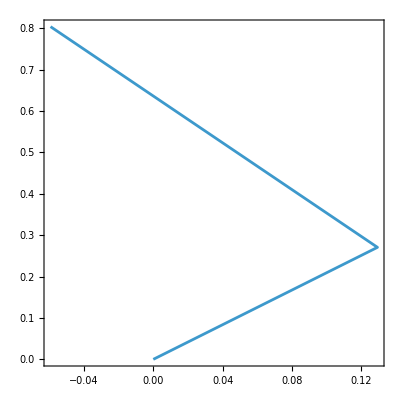

```mathematica
Solve[EQI/.KinSol2[[1]], ψd];
Solve[EQII /. KinSol2[[2]], ψd]; (*Let's pick one of the 2 configurations*)
A = {L1 * Cos[θ1[t]], L1 * Sin[θ1[t]], h, 1};
P1 = {L2 * Cos[θ2[t]], L2 * Sin[θ2[t]], 0, 1};
P = M01.P;
AN = N[A /. KinSol /.Data2];
PN = N[P /. KinSol /.Data2];

ListLinePlot[{{0, 0}, {AN[[1]], AN[[2]]}, {PN[[1]], PN[[2]]}}, Frame -> True, AspectRatio-> 1]
```

## Force Ellipsoid - 16/10/2025

```mathematica
EEc = {EE[[1]], EE[[2]]} /. θ1[t] -> θ1 /. θ2[t] -> θ2;  (*we work on the plane for semplicity and use not time dipendent parameters*)
EEc // MatrixForm
```

(L1 Cos[θ1]+L2 Cos[θ1+θ2]
L1 Sin[θ1]+L2 Sin[θ1+θ2])

```mathematica
Jac = D[EEc, {{θ1, θ2}}]; (*let's use it to understand in which directions the robot looses mobility*)
Jac // MatrixForm
```

(-L1 Sin[θ1]-L2 Sin[θ1+θ2] | -L2 Sin[θ1+θ2]
L1 Cos[θ1]+L2 Cos[θ1+θ2] | L2 Cos[θ1+θ2])

```mathematica
DetJac = Simplify[Det[Jac]] (*The only joint that can cause problems of mobility is theta2, it's impossible to loose mobility cause of theta1*)
```

L1 L2 Sin[θ2]

```mathematica
θ1singular = Solve[Simplify[Det[Jac] == 0], θ1] (*there is no solution because no matter theta1 and we don't fall in a singular position*)
θ2singular = Solve[Simplify[Det[Jac] == 0], θ2]
```

{}

{{θ2→ConditionalExpression[2 π C[1], C[1]∈ℤ]},{θ2→ConditionalExpression[π+2 π C[1], C[1]∈ℤ]}}

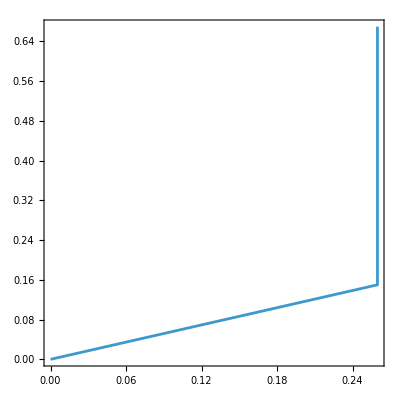

```mathematica
Data = {L1 -> 0.3, L2 -> 0.3, θ1 -> π/6, θ2 -> π/3};
A2 = {A[[1]], A[[2]]} /. θ1[t] -> θ1 /. θ2[t] -> θ2;
P2 = {P[[1]], P[[2]]} /. θ1[t] -> θ1 /. θ2[t] -> θ2;
AN2 = N[A2 /. Data];
PN2 = N[P2 /. Data];

ListLinePlot[{{0, 0}, AN2, PN2}, Frame->True, AspectRatio->1]
```

Typically the budget consists in the torque limit of the motor that is choosen for the application. Now let’s find the ellipsoid.
The ellipsoid comes from the quadratic form and the eigenvalues indicate how much the ellipsoid is stretched, so the axis of its

```mathematica
F = {Fx, Fy};
FM = Simplify[Jac.Transpose[Jac]];
FM // MatrixForm
```

(L2^2 Sin[θ1+θ2]^2+(L1 Sin[θ1]+L2 Sin[θ1+θ2])^2 | -L1^2 Cos[θ1] Sin[θ1]-L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2])
-L1^2 Cos[θ1] Sin[θ1]-L2 (L2 Sin[2 (θ1+θ2)]+L1 Sin[2 θ1+θ2]) | L2^2 Cos[θ1+θ2]^2+(L1 Cos[θ1]+L2 Cos[θ1+θ2])^2)

```mathematica
Fellipse = Simplify[Transpose[F].FM.F - Kf^2] (*This is the function of the ellipsoid*)
```

-Kf^2+Fy^2 L1^2 Cos[θ1]^2+2 Fy^2 L2^2 Cos[θ1+θ2]^2+Fx^2 L1^2 Sin[θ1]^2+2 Fy L1 Cos[θ1] (Fy L2 Cos[θ1+θ2]-Fx L1 Sin[θ1])+2 Fx^2 L1 L2 Sin[θ1] Sin[θ1+θ2]+2 Fx^2 L2^2 Sin[θ1+θ2]^2-2 Fx Fy L2^2 Sin[2 (θ1+θ2)]-2 Fx Fy L1 L2 Sin[2 θ1+θ2]

```mathematica
NumericalMatF = Simplify[FM /. Data /. {Kf -> 1}]; (*tipically we have real numbers for the bufget Kf, but here we normalize it with 1*)
NumericalMatF // MatrixForm
```

(0.2925 | -0.116913
-0.116913 | 0.0675)

```mathematica
EigVecF = Eigenvectors[NumericalMatF];
EigVecF // MatrixForm
EigValF = Eigenvalues[NumericalMatF]
```

(-0.920156 | 0.391551
-0.391551 | -0.920156)

{0.34225,0.0177502}

```mathematica
(*USEFUL COMMANDS*)
Re[EigValF[[1]]]
Norm[EigVecF[[1]]]
(*FINISH*)
```

0.34225

1.

```mathematica
Fellipse /.Data /. {Kf -> 1} (*numerical expression in terms of x and y of the ellipsoid*)
```

-1.+0.2925 Fx^2+0.519615 (0.-0.15 Fx) Fy-0.155885 Fx Fy+0.0675 Fy^2

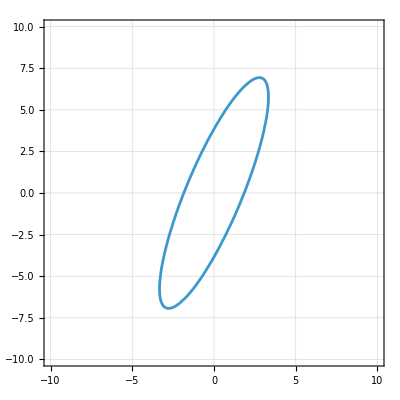

```mathematica
plContourF = ContourPlot[(Fellipse /.Data /. {Kf -> 1}) == 0, {Fx, -10, 10}, {Fy, -10, 10}, GridLines->Automatic] (*For curve levels, round brackets for deciding what to plot*)
```

The ellipsoid tells us in which direction the robot can provide how much force. For the same amount of torque/force, we can get the maximum force among the direction of the major eigenvalue